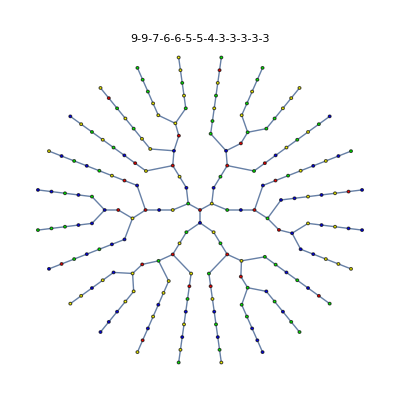
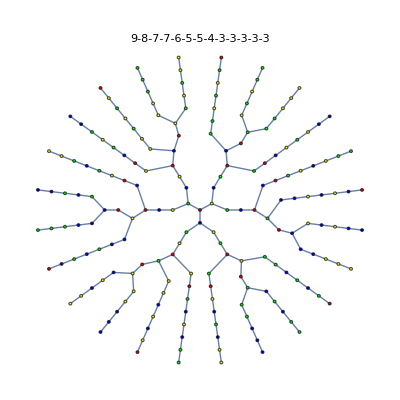
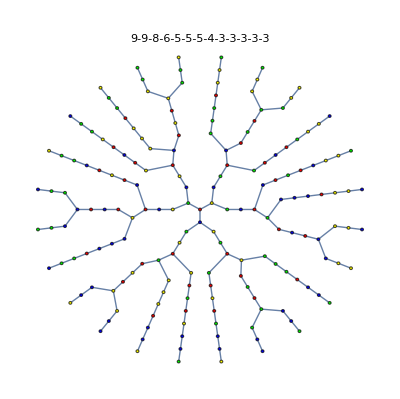
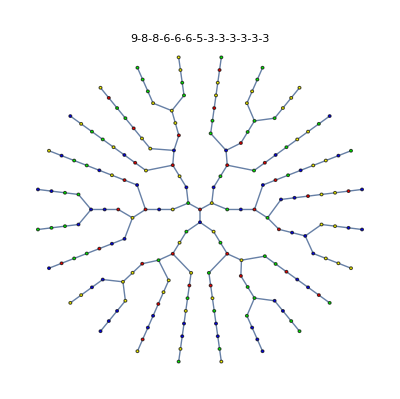
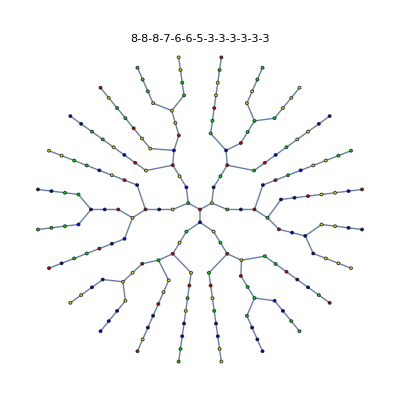
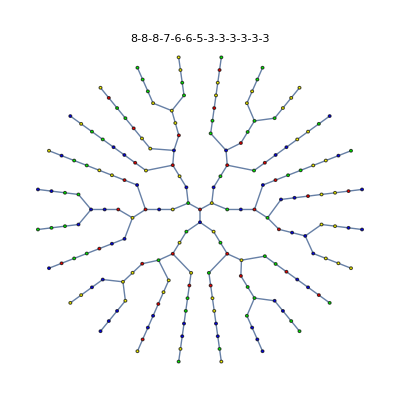
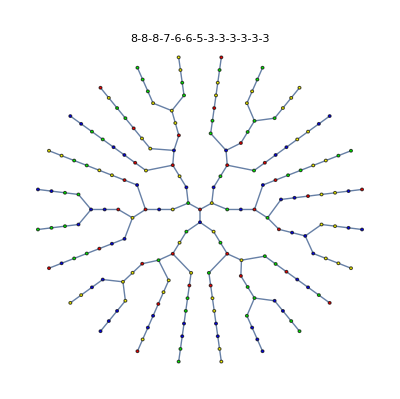
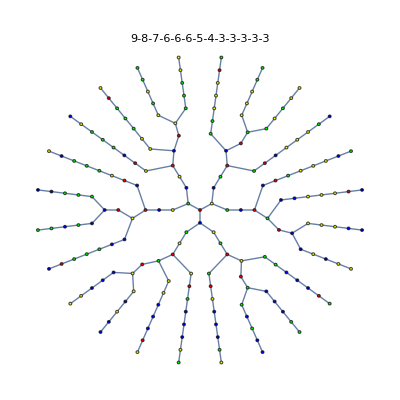

```mathematica
Monitor[Table[
With[
{edges=Map[EdgeList[PathGraph[Map[ToString[#]&,Haccumulate[ RecordToCouples[#]]]]]&,ToVarsLogical[ReadGrof[k],x1==1]]},
With[
{g=Graph[DeleteDuplicates[Flatten[edges]]]},
Graph[g, GraphLayout->"RadialDrawing",VertexStyle->Map[#->IndexToColor[ FromDigits[ StringTake[#,-1]]]&, VertexList[g]], PlotLabel->GraphSignature2[ReadGrof[k]]
]
]
],{k,50000,50010}
],k]
```

```mathematica
EndMPG[[12]]
```

Part::partw: Part 12 of {2, 4, 9, 23, 73, 306, 1555, 9150, 58716, 398438} does not exist.

{2,4,9,23,73,306,1555,9150,58716,398438}⟦12⟧

```mathematica
ToVarsLogical[ReadGrof[58716],x1==1]
```

{{x1→1,x2→2,x3→3,x5→4,x13→1,x4→1,x6→1,x7→1,x8→1,x9→2,x10→2,x11→2,x12→2},{x1→1,x2→2,x3→4,x5→3,x13→1,x4→1,x6→1,x7→1,x8→1,x9→2,x10→2,x11→2,x12→2},{x1→1,x2→3,x3→2,x5→4,x13→1,x4→1,x6→1,x7→1,x8→1,x9→3,x10→3,x11→3,x12→3},{x1→1,x2→3,x3→4,x5→2,x13→1,x4→1,x6→1,x7→1,x8→1,x9→3,x10→3,x11→3,x12→3},{x1→1,x2→4,x3→2,x5→3,x13→1,x4→1,x6→1,x7→1,x8→1,x9→4,x10→4,x11→4,x12→4},{x1→1,x2→4,x3→3,x5→2,x13→1,x4→1,x6→1,x7→1,x8→1,x9→4,x10→4,x11→4,x12→4}}

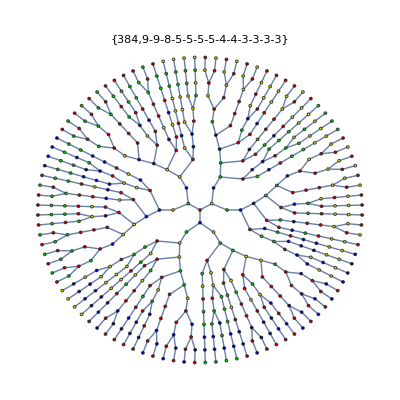
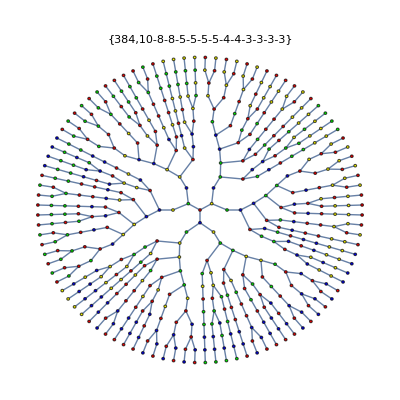
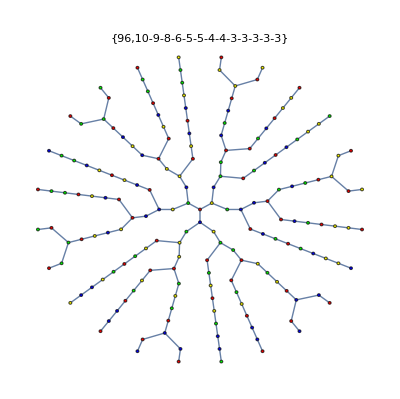
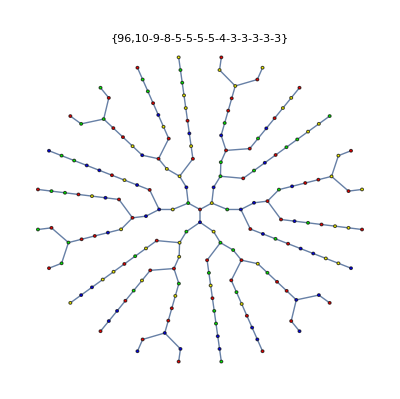
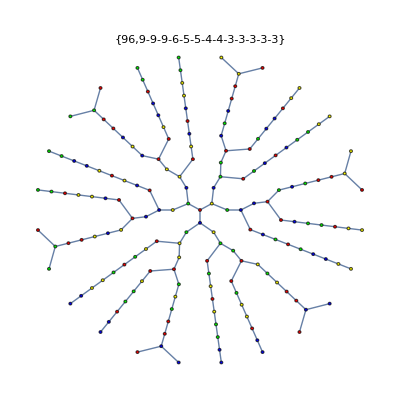
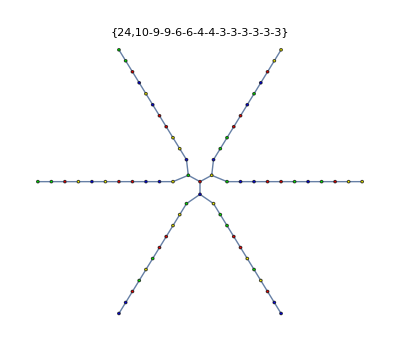
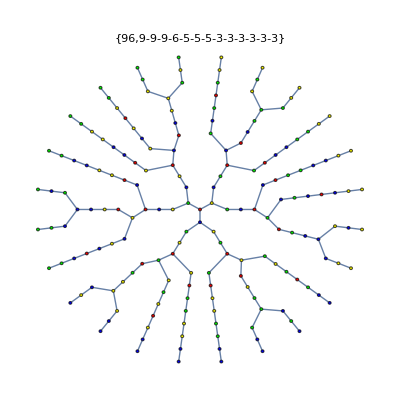
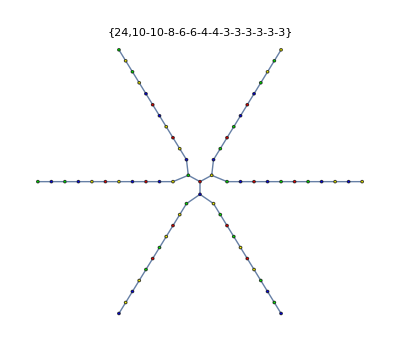

```mathematica
Monitor[Table[
With[
{edges=Map[EdgeList[PathGraph[Map[ToString[#]&,Haccumulate[ RecordToCouples[#]]]]]&,ToVarsLogical[ReadGrof[k],x1==1]]},
With[
{g=Graph[DeleteDuplicates[Flatten[edges]]]},
Graph[g, GraphLayout->"RadialDrawing",VertexStyle->Map[#->IndexToColor[ FromDigits[ StringTake[#,-1]]]&, VertexList[g]], PlotLabel->{Chrom[k],GraphSignature2[ReadGrof[k]]}
]
]
],{k,58716-10,58716}
],k]
```

```mathematica
Map[Symbol["x"<>ToString[#]]&, FindHamiltonianPath[ReadGrof[k],1,VertexCount[ReadGrof[k]]]]
```

```mathematica
SolutionTreeGraph[h_]:=Block[{edges,order},
(* we first take a hamiltonian path to make sure the nodes in the 3 have different colors when they are next to each other *)
order=Map[Symbol["x"<>ToString[#]]&, FindHamiltonianPath[h,1,VertexCount[h]]];
edges=Map[EdgeList[PathGraph[Map[ToString[#]&,Haccumulate[ order/.#]]]]&,ToVarsLogical[h,x1==1]];
With[
{g=Graph[DeleteDuplicates[Flatten[edges]]]},
Graph[g, GraphLayout->"RadialDrawing",VertexStyle->Map[#->IndexToColor[ FromDigits[ StringTake[#,-1]]]&, VertexList[g]], PlotLabel->{ChromaticPolynomial[h,4]/24,GraphSignature2[h]},
ImageSize->400
]
]
]
```

{x1,x2,x3,x4}

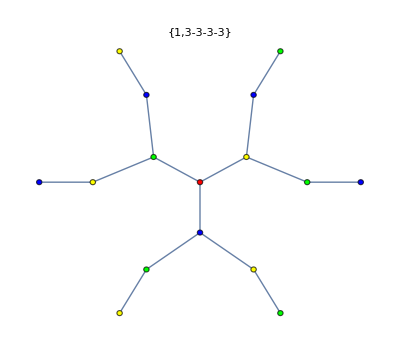

```mathematica
SolutionTreeGraph[JacobsThalGraph2[4]]
```

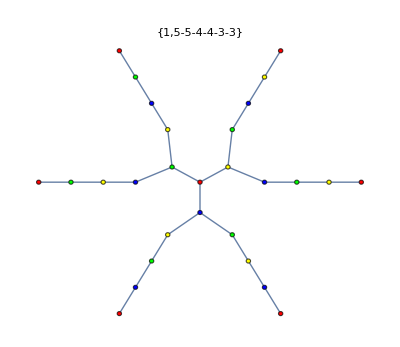
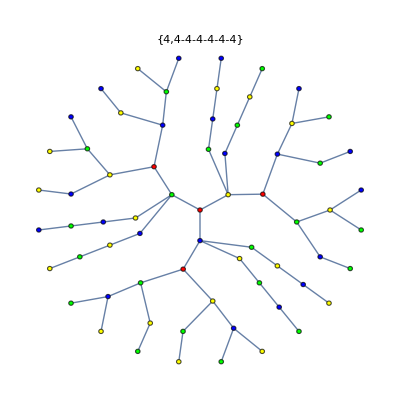
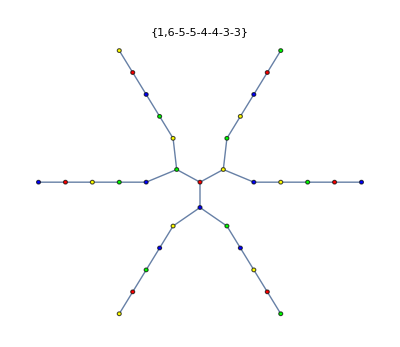
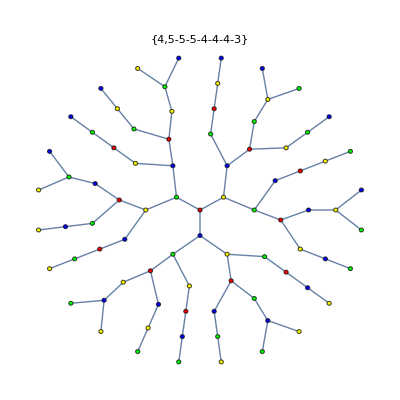
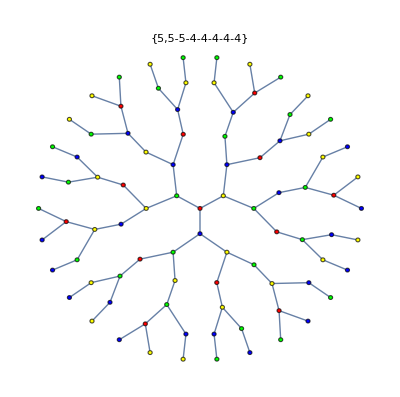
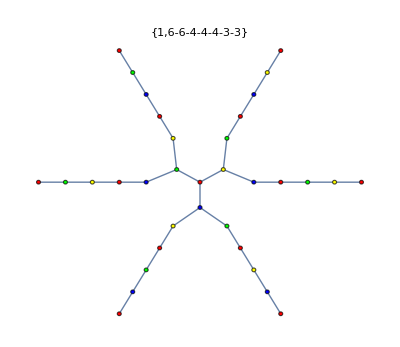

```mathematica
Table[SolutionTreeGraph[ReadGrof[k]],{k,3,8}]
```